```mathematica
Quit[]
```

```mathematica
eq1=D[p[t], t]==c1*p[t]*(1-p[t])-e*p[t];
eq2=D[q[t],t]==c2*q[t]*(1-p[t]-q[t])-c1*p[t]*q[t]-e*q[t];
param={c1->0.3, c2->2.0};
```

```mathematica
rhs1=eq1[[2]]/.{p[t]->P, q[t]->Q}
rhs2=eq2[[2]]/.{p[t]->P, q[t]->Q}
```

-e P+c1 (1-P) P

-e Q-c1 P Q+c2 (1-P-Q) Q

```mathematica
eqVal=SolveValues[{rhs1==0, rhs2==0}, {P,Q}]
(J=D[{rhs1, rhs2}, {{P,Q}}])//MatrixForm
```

{{0,-(-c2+e)/c2},{-(-c1+e)/c1,-(c1^2-c2 e)/(c1 c2)},{0,0},{(c1-e)/c1,0}}

(-e+c1 (1-P)-c1 P | 0
-c1 Q-c2 Q | -e-c1 P+c2 (1-P-Q)-c2 Q)

```mathematica
eqVal1=eqVal/.param
J1=J/.param
```

{{0,-0.5 (-2.+e)},{-3.33333 (-0.3+e),-1.66667 (0.09-2. e)},{0,0},{3.33333 (0.3-e),0}}

{{-e+0.3 (1-P)-0.3 P,0},{-2.3 Q,-e-0.3 P+2. (1-P-Q)-2. Q}}

### Bifurcation diagram for extinction rate parameter e

```mathematica
{eqPointP, eqPointQ, markerList}=Reap[
Do[
{pp,pq,m}=Reap[
Do[
eq=eqVal1[[i]]/.e->j;
Sow[{{j, eq[[1]]}},pop];
Sow[{{j, eq[[2]]}}, poq];
jac=J1/.{P->eq[[1]], Q->eq[[2]], e->j};
re=Re[Eigenvalues[jac]];
ma=If[Max[re]<0, {●,2}, {"-",7}];
Sow[ma, mark],
{j, 0, 4,0.01}]][[2]];
Sow[pp, p];
Sow[pq, q];
Sow[m, marker],
{i, 1, 4}]
][[2]];
```

```mathematica
colorList=Join[{#, Opacity[0.5]}&/@ColorData[97,"ColorList"][[1;;2]],
{#, Opacity[0.2]}&/@ColorData[97,"ColorList"][[3;;4]]]
```

{{RGBColor[0.368417, 0.506779, 0.709798],Opacity[0.5]},{RGBColor[0.880722, 0.611041, 0.142051],Opacity[0.5]},{RGBColor[0.560181, 0.691569, 0.194885],Opacity[0.2]},{RGBColor[0.922526, 0.385626, 0.209179],Opacity[0.2]}}

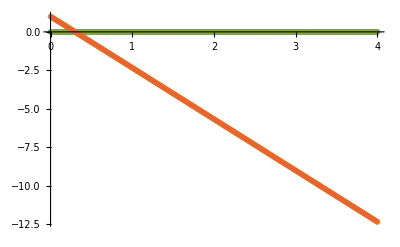

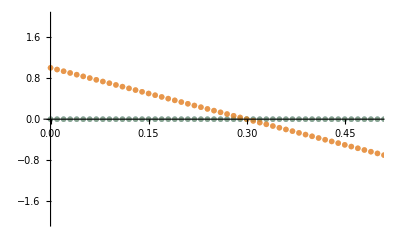

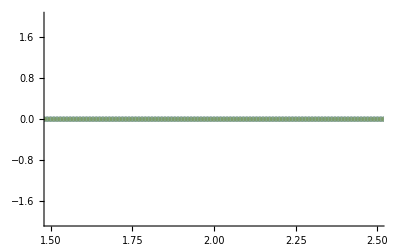

```mathematica
plotP=Table[
ListPlot[eqPointP[[i]], PlotMarkers->markerList[[i]], PlotStyle->{colorList[[i]]}], {i,1,4}];
Show[plotP, PlotRange->Full]
Show[plotP, PlotRange->{{0, 0.5}, {-2,2}}]
Show[plotP, PlotRange->{{1.5, 2.5}, {-2,2}}]
```

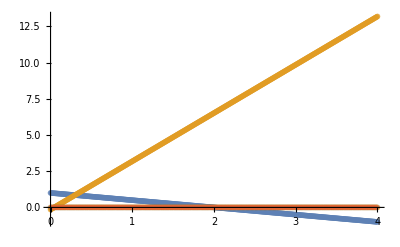

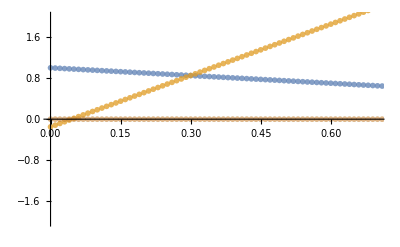

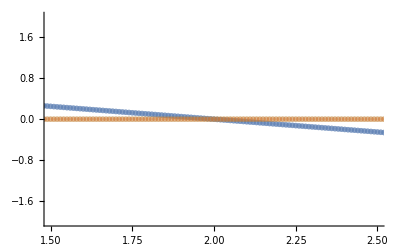

```mathematica
plotQ=Table[
ListPlot[eqPointQ[[i]], PlotMarkers->markerList[[i]], PlotStyle->{colorList[[i]]}], {i,1,4}];
Show[plotQ, PlotRange->Full]
Show[plotQ, PlotRange->{{0, 0.7}, {-2,2}}]
Show[plotQ, PlotRange->{{1.5, 2.5}, {-2,2}}]
```

```mathematica
ei1=Table[Eigenvalues[J1/.{P->eqVal1[[i,1]], Q->eqVal1[[i,2]]}], {i,1,4}]//Simplify
Reduce[ei1[[1,1]]<0&& ei1[[1,2]]<0, e]
Reduce[ei1[[2,1]]<0&& ei1[[2,2]]<0, e]
Reduce[ei1[[3,1]]<0&& ei1[[3,2]]<0, e]
Reduce[ei1[[4,1]]<0&& ei1[[4,2]]<0, e]
```

{{0.3-e,-2.+1. e},{-0.3+1. e,0.3-6.66667 e},{0.3-e,2.-e},{-0.3+1. e,-0.3+6.66667 e}}

0.3<e<2.

0.045<e<0.3

e>2.

e<0.045

Therefore, there are 3 bifurcation points at: e==0.045, e==0.3, and e==2.0.

### Bifurcation in the 2D (e,c_2) parameter space

```mathematica
eqVal2=eqVal/.c1->0.3
(J2=J/.c1->0.3)//MatrixForm
```

{{0,-(-c2+e)/c2},{-3.33333 (-0.3+e),-(3.33333 (0.09-c2 e))/c2},{0,0},{3.33333 (0.3-e),0}}

(-e+0.3 (1-P)-0.3 P | 0
-0.3 Q-c2 Q | -e-0.3 P+c2 (1-P-Q)-c2 Q)

```mathematica
ei2=Table[Eigenvalues[J2/.{P->eqVal2[[i,1]], Q->eqVal2[[i,2]]}], {i,1,4}]//Simplify
```

{{-1. (c2-1. e),-1. (-0.3+e)},{-0.3+1. e,0.3-3.33333 c2 e},{0.3-e,c2-e},{-0.3+1. e,-0.3+3.33333 c2 e}}

```mathematica
Reduce[ei2[[1,1]]<0&& ei2[[1,2]]<0, {e, c2}]
Reduce[ei2[[2,1]]<0&& ei2[[2,2]]<0, {e, c2}]
Reduce[ei2[[3,1]]<0&& ei2[[3,2]]<0, {e, c2}]
Reduce[ei2[[4,1]]<0&& ei2[[4,2]]<0, {e, c2}]
```

e>0.3&&c2>e

(e<0&&c2<0.09/e)||(0<e<0.3&&c2>0.09/e)

e>0.3&&c2<e

c2∈ℝ&&((e<0&&c2>0.09/e)||e==0||(0<e<0.3&&c2<0.09/e))

Bifurcation points for the 1st and 3rd equilibrium are where e==0.3 and c2==e. When e==0.3, either c2>0.3 or c2<0.3, there is always a equilibrium point to switch to. However, when c2==e, then c2==e>0.3 so that the equilibrium points can exchange. We have when c2==e<0.3, the 4th equilibrium is stable, because c2=e<0.09/e when e<√0.09=0.3 
Bifurcation points for 2nd and 4th equilibrium are where e==0.3 and c2==0.09/e. Similarly, when e==0.3, either c2>0.3 or c2<0.3, there is always a equilibrium point to switch to. However, when c2==0.09/e, then c2==0.09/e>0.09/0.3=0.3 so that the equilibrium points can exchange. We have when c2==0.09/e<0.3, the 3rd equilibrium is stable, because c2=0.09/e<e when e>√0.09=0.3

Just looking at the conditions for stability, we can also deduce that:
- Bifurcation at e==0.3, since for e>0.3, either 1st or 3rd equilibrium is stable, while for e<0.3, either 2nd or 4th equilibrium is stable.
- For e>0.3, bifurcation at c2==e>0.3, since for c2>e, 1st equilibrium is stable, while for c2<e, 3rd equilibrium is stable.
- Likewise for e<0.3, bifurcation at c2==0.09/e>0.3, since for c2>0.09/e, 2nd equilibrium is stable, while for c2<0.09/e, 4th equilibrium is stable.

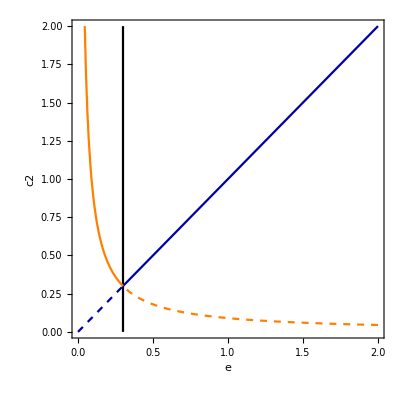

```mathematica
p1=ContourPlot[e==0.3,{e, 0,2},{c2,0,2}, ContourStyle->Black];
p2a=ContourPlot[{c2==e, c2==0.09/e}, {e,0, 2}, {c2, 0.3, 2}, ContourStyle->{Darker[Blue], Orange}];
s={#,Dashed}&/@{Darker[Blue], Orange};
p2b=ContourPlot[{c2==e, c2==0.09/e}, {e,0,2}, {c2, 0, 0.3}, ContourStyle->s];

Show[{p1, p2a, p2b}, Frame->True, FrameLabel->{Style["e", FontSize->12],Style["c2", FontSize->12]}]
```

When c_2 falls below the value of c_1, species 2 can never persist in the metapopulation with species 1: it always loses competition and it is also slower to disperse when c_2<c_1. Therefore, we find only two parameter regimes below  c_2=c_1. So now we have that for c2<c1=0.3, there are two regimes corresponding to the 3rd and the 4th equilibrium can exist. We see that the 3rd equilibrium is stable for e>0.3 and the 4th equilibrium is stable for e<0.3.

```mathematica
{points, coList}=Reap[
Do[
Sow[{{i,j}},p];
Do[
If[Max[ei2[[k]]/.{e->i, c2->j}]<0,c=ColorData[97,"ColorList"][[k]]; Break[],Continue[]],
{k,1,4}];
Sow[c, col],
{i, 0,2,0.1}, {j,0,2,0.1}]
][[2]];
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179]}

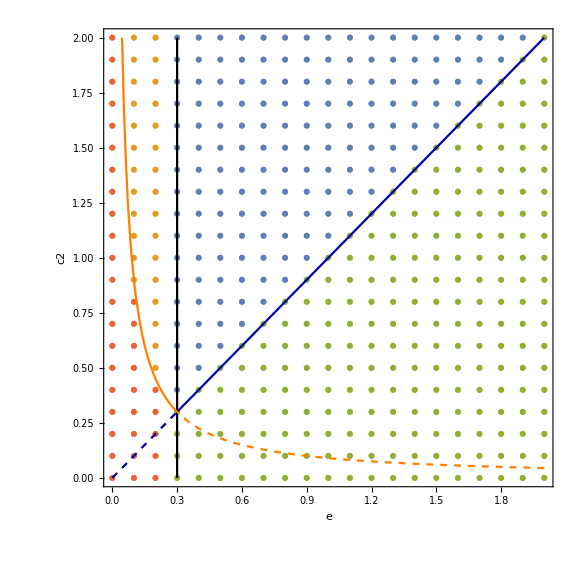

```mathematica
p3=ListPlot[points, PlotStyle->coList];
ColorData[97,"ColorList"][[1;;4]]
Show[{p3,p1, p2a, p2b}, Frame->True, FrameLabel->{Style["e", FontSize->12],Style["c2", FontSize->12]}, ImageSize->Large, AspectRatio->1.0]
```